## Physics 449 hw#5 Due Mar 23 W9F

Name: Ruojun Wang 
Date: Mar 18 W9Sun

```mathematica
<<"http://www.physics.wisc.edu/~tgwalker/448defs.m"
```

## 1) T 11.10

### Unperturbed Energies

```mathematica
{Sx,Sy,Sz}=angmom[1]
```

{{{0,1/(√2),0},{1/(√2),0,1/(√2)},{0,1/(√2),0}},{{0,-ⅈ/(√2),0},{ⅈ/(√2),0,-ⅈ/(√2)},{0,ⅈ/(√2),0}},{{1,0,0},{0,0,0},{0,0,-1}}}

```mathematica
H0ion=a/ℏ^2 Sz.Sz;
{evaH0ion,eveH0ion}=Eigensystem[H0ion]
```

{{a/ℏ^2,a/ℏ^2,0},{{0,0,1},{1,0,0},{0,1,0}}}

The unperturbed energies are a/ℏ^2,a/ℏ^2,0.

### The 1st-Order corrections

```mathematica
H1ion=b/ℏ^2(Sx.Sx-Sy.Sy);
Matrix1={{eveH0ion⟦1⟧.H1ion.eveH0ion⟦1⟧, eveH0ion⟦1⟧.H1ion.eveH0ion⟦2⟧, eveH0ion⟦1⟧.H1ion.eveH0ion⟦3⟧}, {eveH0ion⟦2⟧.H1ion.eveH0ion⟦1⟧, eveH0ion⟦2⟧.H1ion.eveH0ion⟦2⟧, eveH0ion⟦2⟧.H1ion.eveH0ion⟦3⟧}, {eveH0ion⟦3⟧.H1ion.eveH0ion⟦1⟧, eveH0ion⟦3⟧.H1ion.eveH0ion⟦2⟧, eveH0ion⟦3⟧.H1ion.eveH0ion⟦3⟧}}
```

{{{{0}},{{b/ℏ^2}},{{0}}},{{{b/ℏ^2}},{{0}},{{0}}},{{{0}},{{0}},{{0}}}}

```mathematica
{evaM1,eveM1}=Eigensystem[{{0, b/ℏ^2, 0}, {b/ℏ^2, 0, 0}, {0, 0, 0}}]
```

{{-b/ℏ^2,b/ℏ^2,0},{{-1,1,0},{1,1,0},{0,0,1}}}

The first order corrections are -b/ℏ^2,b/ℏ^2,0.

### Compare to the exact results

```mathematica
Hion=H0ion+H1ion
```

{{a/ℏ^2,0,b/ℏ^2},{0,0,0},{b/ℏ^2,0,a/ℏ^2}}

```mathematica
Eigensystem[Hion]
```

{{0,(a-b)/ℏ^2,(a+b)/ℏ^2},{{0,1,0},{-1,0,1},{1,0,1}}}

The eigenstates are {-1,0,1},{1,0,1}; eigenvalues are (a-b)/ℏ^2,(a+b)/ℏ^2. It matches with the exact results.

## 2) T 11.11

(Ĥ)_0=((p̂)_x)^2/(2m)+1/2 m ω^2(x̂)^2+((p̂)_y)^2/(2 m)+1/2 m ω^2(ŷ)^2; (Ĥ)_1=b x̂ ŷ 
The first-order energy shifts to the ground state is given by φ_n^0(Ĥ)_1 φ_n^0=φ_n^0b x̂ ŷ φ_n^0

Given by (7.11), x̂=√(ℏ/(2 m ω_x))(â+(â)^†); ŷ=√(ℏ/(2 m ω_y))(â+(â)^†);(p̂)_x=-ⅈ √((m ω_x ℏ)/2)(â-(â)^†);(p̂)_y=-ⅈ √((m ω_y ℏ)/2)(â-(â)^†) 

To obtain the eigenvectors and eigenvalues of (Ĥ)_0:
(Ĥ)_0 n=((p̂)_x)^2/(2m)n+1/2 m ω^2(x̂)^2 n+((p̂)_y)^2/(2 m)n+1/2 m ω^2(ŷ)^2 n

	((p̂)_x)^2/(2m)n=(m ω_x ℏ)/2((â-(â)^†)^2)/(2m)n=(ω_x ℏ)/4((â)^2-â(â)^†-N̂+((â)^†)^2)n
		â n=√n n-1; (â)^†n=√(n+1)n+1
		→ (â)^2 n=√(n (n-1))n-2; â(â)^†n=(n+1)n; N̂ n=nn; ((â)^†)^2 n=√((n+1)(n+2))n+2
	→ ((p̂)_x)^2/(2m)n=(ω_x ℏ)/4(√(n (n-1))n-2-n+√((n+1)(n+2))n+2)

	1/2 m ω^2(x̂)^2 n=1/2 m ω_x^2 ℏ/(2 m ω_x)(â+(â)^†)^2 n=(ω_x ℏ)/4((â)^2+â(â)^†+N̂+((â)^†)^2)n=(ω_x ℏ)/4(√(n (n-1))n-2+(2n+1)n+√((n+1)(n+2))n+2)

→ (Ĥ)_0 n=(ω_x ℏ)/4(√(n (n-1))n-2-n+√((n+1)(n+2))n+2+√(n (n-1))n-2+(2n+1)n+√((n+1)(n+2))n+2)+(ω_y ℏ)/4(√(n (n-1))n-2-n+√((n+1)(n+2))n+2+√(n (n-1))n-2+(2n+1)n+√((n+1)(n+2))n+2)
=((ω_x ℏ)/4+(ω_y ℏ)/4)(4 √(n (n-1))n-2+4 √((n+1)(n+2))n+2+4nn)
=ℏ (ω_x +ω_y)(√(n (n-1))n-2+√((n+1)(n+2))n+2+nn)

The eigenstates are n,n+2,n-2.


φ_n^0(Ĥ)_1 φ_n^0=φ_n^0b x̂ ŷ φ_n^0

n(Ĥ)_1 n=nb √(ℏ/(2 m ω_x))(â+(â)^†)√(ℏ/(2 m ω_y))(â+(â)^†)n=b ℏ/(2 m)√(1/(ω_x ω_y))n((â)^2+â(â)^†+(â)^†â+((â)^†)^2)n=b ℏ/(2 m)√(1/(ω_x ω_y))n((â)^2+â(â)^†+N̂+((â)^†)^2)n
=b ℏ/(2 m)√(1/(ω_x ω_y))(n(â)^2 n+n â(â)^†n+n N̂ n+n((â)^†)^2 n)=b ℏ/(2 m)√(1/(ω_x ω_y))(n(â)^2 n+n â(â)^†n+n N̂ n+n((â)^†)^2 n)
=b ℏ/(2 m)√(1/(ω_x ω_y))(n √(n (n-1))n-2+n(n+1)n+nnn+n √((n+1) (n+2))n+2)=b ℏ/(2 m)√(1/(ω_x ω_y))(2n+1)

Similarly, n(Ĥ)_1 n+2=b ℏ/(2 m)√(1/(ω_x ω_y))√(n (n-1)); n(Ĥ)_1 n-2=b ℏ/(2 m)√(1/(ω_x ω_y))√((n+1) (n+2))
n+2(Ĥ)_1 n=b ℏ/(2 m)√(1/(ω_x ω_y))√((n+1) (n+2)); n+2(Ĥ)_1 n+2=b ℏ/(2 m)√(1/(ω_x ω_y))(2n+1);  n+2(Ĥ)_1 n-2=0
n-2(Ĥ)_1 n=b ℏ/(2 m)√(1/(ω_x ω_y))√(n (n-1)); n-2(Ĥ)_1 n+2=0;  n-2(Ĥ)_1 n-2=b ℏ/(2 m)√(1/(ω_x ω_y))(2n+1)

Hence, the perturbing Hamiltonian in the subspace of degenerate states is (Ĥ)_1=b ℏ/(2 m)√(1/(ω_x ω_y))(2n+1 | √(n (n-1)) | √((n+1) (n+2))
√((n+1) (n+2)) | 2n+1 | 0
√(n (n-1)) | 0 | 2n+1)

```mathematica
Eigenvalues[{{2n+1, √(n (n-1)), √((n+1) (n+2))}, {√((n+1) (n+2)), 2n+1, 0}, {√(n (n-1)), 0, 2n+1}}]//FullSimplify
```

{1+2 n,1+2 n-√2 ((-1+n) n)^(1/4) ((1+n) (2+n))^(1/4),1+2 n+√2 ((-1+n) n)^(1/4) ((1+n) (2+n))^(1/4)}

```mathematica
f[n_]:={1+2 n,1+2 n-√2 ((-1+n) n)^(1/4) ((1+n) (2+n))^(1/4),1+2 n+√2 ((-1+n) n)^(1/4) ((1+n) (2+n))^(1/4)}

f[0]
f[1]
```

{1,1,1}

{3,3,3}

The first-order energy shifts to the ground state are b ℏ/(2 m)1/ω
The degenerate first excited states due to the perturbation are 3b ℏ/(2 m)1/ω

## 3-4) A 131-Xe nucleus, spin k=3/2, has the Hamiltonian H=-μ B K_z+Q  K_x^2-5/4.

```mathematica
{Kx,Ky,Kz}=angmom[3/2];
```

```mathematica
HXe=-μ B Kz+Q(Kx.Kx-5/4 IdentityMatrix[4]);
```

```mathematica
HXe0=-μ B Kz;HXe0//MatrixForm
{evaHXe0,eveHXe0}=Eigensystem[HXe0]
eveHXe0a=Normalize/@eveHXe0//FullSimplify
```

(-(3 B μ)/2 | 0 | 0 | 0
0 | -(B μ)/2 | 0 | 0
0 | 0 | (B μ)/2 | 0
0 | 0 | 0 | (3 B μ)/2)

{{-(3 B μ)/2,(3 B μ)/2,-(B μ)/2,(B μ)/2},{{1,0,0,0},{0,0,0,-1},{0,-1,0,0},{0,0,1,0}}}

{{1,0,0,0},{0,0,0,-1},{0,-1,0,0},{0,0,1,0}}

```mathematica
E0={-(3 μB)/2,-μB/2,μB/2,(3 μB)/2};
```

```mathematica
HXe1=Q(Kx.Kx-5/4 IdentityMatrix[4]);HXe1//MatrixForm
```

(-Q/2 | 0 | (√3 Q)/2 | 0
0 | Q/2 | 0 | (√3 Q)/2
(√3 Q)/2 | 0 | Q/2 | 0
0 | (√3 Q)/2 | 0 | -Q/2)

The first order energy shift is {-Q/2,Q/2,Q/2,-Q/2}
Hence, the perturbed Hamiltonian is  (0 | 0 | (√3 Q)/2 | 0
0 | 0 | 0 | (√3 Q)/2
(√3 Q)/2 | 0 | 0 | 0
0 | (√3 Q)/2 | 0 | 0)

The perturbed Hamiltonian has degenerate eigenvalues. To get the correct first-order shifts

The energy shift to second order in Q is given by E_n^(2)=φ_n^(0)(Ĥ)_1 φ_n^(1)=∑_(k≠n) (φ_n^(0)(Ĥ)_1 φ_k^(0)φ_k^(0)(Ĥ)_1 φ_n^(0))/(E_n^(0)-E_k^(0))

```mathematica
E1Shift3={-Q/2,Q/2,Q/2,-Q/2};
HXe1b={{0, 0, (√3 Q)/2, 0}, {0, 0, 0, (√3 Q)/2}, {(√3 Q)/2, 0, 0, 0}, {0, (√3 Q)/2, 0, 0}};
```

```mathematica
(* evaHXe0={-(3 B μ)/2,(3 B μ)/2,-(B μ)/2,(B μ)/2} *)

E2Shift3=Table[Sum[If[i≠ j,HXe1b⟦i,j⟧^2/(E0⟦i⟧-E0⟦j⟧),0],{j,4}],{i,4}]//FullSimplify
```

{-(3 Q^2)/(8 μB),-(3 Q^2)/(8 μB),(3 Q^2)/(8 μB),(3 Q^2)/(8 μB)}

```mathematica
evaHXe0+E1Shift3+E2Shift3
```

{-Q/2-(3 B μ)/2-(3 Q^2)/(8 μB),Q/2+(3 B μ)/2-(3 Q^2)/(8 μB),Q/2-(B μ)/2+(3 Q^2)/(8 μB),-Q/2+(B μ)/2+(3 Q^2)/(8 μB)}

## 5) Rb atom. Calculate the shift in energy of the 5s state. You may assume that only the 5p excited state contributes to the shift. The wavelength of a 5p→5s photon is 785 nm

H_1=V=e z ε

By the Stark Effect, E_1^(1)=e ε1,0,0z1,0,0=0; E_1^(2)=∑_(n≠1,l,m) (e^2 ε^2|n,l,mz1,0,0|^2)/(E1^(0)-E_n^(0)).........(*1)
The radial matrix element is ∫ⅆr P_(5s)(r) r P_(5p)(r)=5.1.........(*2)
Hence, (*2) has 5,1,0 H_1 5,0,0=e^2 ε^2∫_0^∞ r^2 ⅆr∫_0^π Sin[θ]ⅆθ∫_0^(2π) ⅆϕ (R_(5,1))^*(Y_(5,0))^*r Cos[θ](R_(5,0))^*Y_(5,0) 
(*1) has =-(e^2 ℰ^2)/(3((E_(5,1))^(0)-(E_(5,0))^(0)))(∫ⅆr P_(5,0)(r) r P_(5,1)(r))^2

The values from NIST:
	(E_(5s))^(0)=-1/2×0.30701 Hartrees=-0.153505 Hartrees, (E_(5p))^(0)=(E_(5s))^(0)+1/2×(0.114627827+0.116792952)/2 Hartrees=-0.0956498 Hartrees

```mathematica
-1/2×0.30701
```

-0.153505

```mathematica
-1/2×0.30701+1/2×(0.114627827+0.116792952)/2
```

-0.0956498

To obtain the wavefunctions for 5s,5p states:

```mathematica
P5s=p5s/.NDSolve[{-1/2 p5s''[r]-1/r p5s[r]== -0.153505p5s[r],p5s[30]==1,p5s'[30]==-1},p5s,{r,30,1}]//First;
P5p=p5p/.NDSolve[{-1/2 p5p''[r]+(2/(2 r^2)-1/r)p5p[r]==-0.09564980525  p5p[r],p5p[30]==1,p5p'[30]==-1},p5p,{r,30,1}]//First;
```

The radial matrix element is is ∫ⅆr P_(5s)(r) r P_(5p)(r)=5.1 a_0

```mathematica
NIntegrate[P5p[r]r P5s[r],{r,1,30}]/(√(NIntegrate[P5p[r]^2,{r,1,30}]NIntegrate[P5s[r]^2,{r,1,30}]))
```

5.34355

(*1) has =-(e^2 ℰ^2)/(3((E_(5,1))^(0)-(E_(5,0))^(0)))(∫ⅆr P_(5,0)(r) r P_(5,1)(r))^2

```mathematica
EShift5=1/3(√(14.4 eV Å) ℰ)^2/(0-1.59 eV)(5.343551543297176 0.5292 Å)^2
```

-24.1404 Å^3 ℰ^2

## 6) Plot the energies of the 1s and 2s states of antihydrogen, as a function of magnetic field.

H_hyp=(8π)/3 δ(r)μ_s·μ_p
μ_s=g_s μ_B S; μ_p=g_p μ_N I

→ H_hyp=(8π)/3 δ(r)g_s μ_B S·g_p μ_N I=(8π)/3 δ(r)g_s μ_B S·g_p m_e/m_p μ_B I
→E_hyp=ψ H_hyp ψ

```mathematica
ψ1s=1/(√(4π Subscript[a, 0]^3))*(Subscript[P, 1,0][r])/r
```

ⅇ^-r/(√π √(a_0^3))

```mathematica
ψ2s=1/(√(4π Subscript[a, 0]^3))*(Subscript[P, 2,0][r])/r
```

(ⅇ^(-r/2) (-2+r))/(4 √(2 π) √(a_0^3))

```mathematica
Ehyp={ⅇ^-r/(√π √((0.5292 Å)^3))(8π 5.586*2)/3 0.511/938.28((√(14.4 eV Å) 1973 eV Å)/(2 *511000 eV))^2 ⅇ^-r/(√π √((0.5292 Å)^3)),(ⅇ^(-r/2) (-2+r))/(4 √(2 π) √((0.5292 Å)^3))(8π 5.586*2)/3 0.511/938.28((√(14.4 eV Å) 1973 eV Å)/(2 *511000 eV))^2(ⅇ^(-r/2) (-2+r))/(4 √(2 π) √((0.5292 Å)^3))}/.{r->0}//PowerExpand//N
```

{5.87548×10^-6 eV,7.34435×10^-7 eV}

```mathematica
S6=angmom[1/2];I6=angmom[1/2];
```

E_(1s)=ψ_(1s)E_hyp+2 μ_B B ·S_zψ_(1s). Similarly for E_(2 s).

```mathematica
Energy1s=Eigenvalues[Ehyp⟦1⟧ Sum[S6⟦i⟧⊗I6⟦i⟧,{i,3}]+2 Subscript[μ, B]*B S6⟦3⟧⊗IdentityMatrix[2]/.{Subscript[μ, B]->5.788381  10^-5 eV/T,B-> 1 T bb}]*(8065 *30)/eV//FullSimplify
```

{0.355393-14.005 bb,0.355393+14.005 bb,-0.355393-0.000405331 √(3.07509×10^6+1.19384×10^9 bb^2),0.000405331 (-876.797+√(3.07509×10^6+1.19384×10^9 bb^2))}

```mathematica
Energy2s= Eigenvalues[Ehyp⟦2⟧ Sum[S6⟦i⟧⊗I6⟦i⟧,{i,3}]+2 Subscript[μ, B] B S6⟦3⟧⊗IdentityMatrix[2]/.{Subscript[μ, B]->5.788381  10^-5 eV/T,B-> 1 T bb}]*(8065  30)/eV//FullSimplify
```

{0.0444241-14.005 bb,0.0444241+14.005 bb,-0.0444241-0.000405331 √(48048.4+1.19384×10^9 bb^2),0.000405331 (-109.6+√(48048.4+1.19384×10^9 bb^2))}

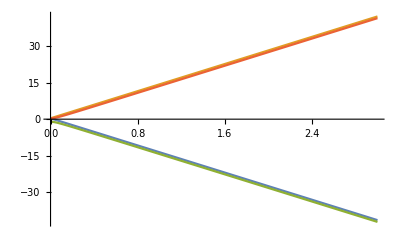

```mathematica
Plot[Energy1s,{bb,0,3}]
```

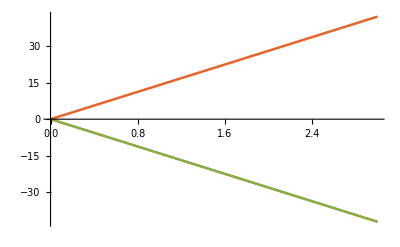

```mathematica
Plot[Energy2s,{bb,0,3}]
```